-Graphics-
Určete minimální hodnotu rezistoru R1 pro obvod na obrázku, za předpokladu,že  stejnosměrný zdroj U1 = 12V, úbytek napětí na diodě je uD = 2V a maximální povolený proud diodou je iD = 20mA.

```mathematica
ClearAll["Global`*"]

u1=12;
uD=2;
iD=20*10^-3;
uR1=u1-uD;
R1=uR1/iD
```

500

Elektrický ohřívač není nic jiného nežli výkonový rezistor na který fouká ventilátor. Tento ventilátor má 4 výkonové režimy  "25%", "50%", "75%" a turbo režim, kdy ohřívač jede na "100%" výkonu.
Na štítku má napsáno, že  při napětí Ueff=230 V má maximální výkon 750 W. 
Jak velký proud,spotřebováná pokud je zapnutý na poloviční chod?
Jaký odpor ohřívač má?
Jak se změní výkon ohřívače,pokud na zimu pojedeme do USA, kde je napětí v síti Ueff =120V? Na jakou hodnotu přitom vzroste maximální proud při maximálním výkonu?

```mathematica
ClearAll["Global`*"]
UefCR=230;
Peloh=750;
(*proud na polovicni vykon*)
Ieloh=(Peloh/2)/UefCR//N

(*odpor*)
Reloh=UefCR/(Peloh/UefCR)//N
(*vykon v USA*)
UefUSA=120;
PelohUSA=UefUSA^2/Reloh
IelohUSA=PelohUSA/UefUSA//N
```

1.63043

70.5333

204.159

1.70132

-Graphics-
Určete celkové zesílení/útlum v dB a přenos pro zapojení, které je na obrázku, pokud mají jednotlivé prvky tyto parametry:
Zesilovač 1 - vstupní signál zesílí 20x,
Zesilovač 2 - vstupní signál zesílí 30x,
Obvod - vstupní signál utlumí 12x,(nápověda:čili vydělí 12)
K1 - kabel, který vstupní signál utlumí 18x,
K2 - kabel, který vstuní signál utlumí 6x
(Nápověda: Zisk je kladný, útlum je záporný)

```mathematica
ClearAll["Global`*"]
x=20*1/18*1/12*1/6*30
decibely = 20*Log10[x]//N
```

25/54

-6.68908

-Graphics-
Určete napětí U2, proudy IC1,IR1 a IR2, pokud:
střídavý zdroj napětí má sinusový průběh s amplitudou Umax = 5V a frekvencí f= 1kHz,
C1 = 100nF,
R1 = 5kΩ,
R2 = 10 kΩ
zesilovací činitel Aoz = 10000

{iC1[t]+iU[t]==0,iR1[t]==iC1[t],iR1[t]==iR2[t],u3[t]-u4[t]==R1 iR1[t],-u2[t]+u4[t]==R2 iR2[t],iC1[t]==C1 (u1'[t]-u3'[t]),u2[t]==-Aoz u4[t],uZ[t]==u1[t],u1[0]==0,u3[0]==0}

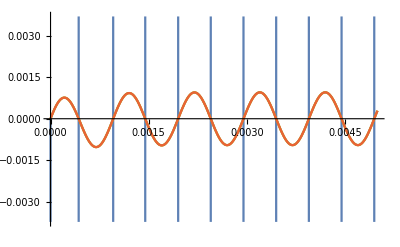

```mathematica
ClearAll["Global`*"]
rovnice={
iU[t]+iC1[t]==0,
iR1[t]==iC1[t],
iR1[t]==iR2[t],
u3[t]-u4[t]==iR1[t]*R1,
u4[t]-u2[t]==iR2[t]*R2,
iC1[t]==C1*(u1'[t]-u3'[t]),
u2[t]==-u4[t]*Aoz,
uZ[t]==u1[t],
u1[0]==0,
u3[0]==0
}

soucastky={R1->5*10^3, R2->10*10^3, C1->100*10^-9, Aoz->10*10^3};
nezname={u1[t], u2[t], u3[t], u4[t], iR1[t], iR2[t], iU[t], iC1[t]};

Umax=5;
frekvence = 1000;
perioda=1/frekvence;
tmax=5*perioda;
uZ[t_]:=Umax*Sin[2*π*frekvence*t];

reseni = NDSolve[rovnice/.soucastky, nezname, {t, 0, tmax}, Method->{"IndexReduction" -> Automatic}, StartingStepSize->10^-12];
Plot[{u2[t]/.reseni, iR1[t]/.reseni, iR2[t]/.reseni, iC1[t]/.reseni}, {t, 0 ,tmax}]
```

-Graphics-
Hodnoty součástek:
R1=R2=0.1 Ω,
R3=R4=1000 Ω,
L1=L2=1 mH,
C1=C2=1 μF.
Vykreslete přenos obvodu pro 1≤ω≤10^8.

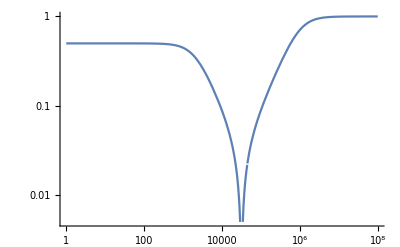

```mathematica
ClearAll["Global`*"]
R1=R2=0.1;
R3=R4=1000;
L1=L2=1*10^-3;
C1=C2=1*10^-6;

ZR1=R1;
ZR2=R2;
ZR3=R3;
ZR4=R4;
ZL1=ⅉ*ω*L1;
ZL2=ⅉ*ω*L2;
ZC1=1/(ⅉ*ω*C1);
ZC2=1/(ⅉ*ω*C2);
ZR1C1=ZR1+ZC1;
ZR2L1=ZR2+ZL1;
ZR1C1R2L1=(ZR1C1*ZR2L1)/(ZR1C1+ZR2L1) ;
ZR1C1R2L1R3=ZR1C1R2L1+ZR3;
ZC2R4=(ZC2*ZR4)/(ZC2+ZR4);
ZC2R4L2=ZC2R4+ZL2;
Prenos=ZC2R4L2/(ZR1C1R2L1R3+ZC2R4L2);
LogLogPlot[Abs[Prenos],{ω, 1, 10^8}]
```